### Exercises 5 and 6 of Chapter 01 from “Dynamical Systems with Applications using Python”

#### 5. Evaluate the following limits if they exist:

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[(x^3+3 x^2-5)/(2 x^3-7*x),x->Infinity]
```

1/2

```mathematica
Limit[(Cos[x]+1)/(x-π),x->π]
```

0

```mathematica
Limit[1/x,x->0,Direction->"FromAbove"]
```

∞

```mathematica
Limit[(2Sinh[x]-2Sin[x])/(Cosh[x]-1),x->0]
```

0

#### 6. Find the derivatives of the following functions

```mathematica
f[x_]=3 x^3+2 x^2-5;
f'[x]
```

4 x+9 x^2

```mathematica
f[x_]=√(1+x^4);
f'[x]
```

(2 x^3)/(√(1+x^4))

```mathematica
f[x_]=Exp[x]Sin[x]Cos[x];
f'[x]
```

ⅇ^x Cos[x]^2+ⅇ^x Cos[x] Sin[x]-ⅇ^x Sin[x]^2

```mathematica
f[x_]=Tanh[x];
f'[x]
```

Sech[x]^2

```mathematica
f[x_]=x^Log[x];
f'[x]
```

2 x^(-1+Log[x]) Log[x]

#### Evaluate the following definite integrals:

```mathematica
Integrate[3 x^3+2 x^2-5,{x,0,1}]
```

-43/12

```mathematica
Integrate[1/x^2,{x,1,Infinity}]
```

1

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[1/(√x),{x,0,1}]
```

2

```mathematica
Integrate[Sin[1/t]/t^2,{t,0,2/π}]
```

Integrate::idiv: Integral of Sin[1/t]/t^2 does not converge on {0,2/π}.

∫_0^(2/π) Sin[1/t]/t^2 ⅆt

#### 7. Graph the following:

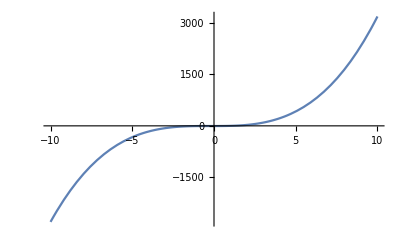

```mathematica
Plot[3 x^3+2 x^2-5,{x,-10,10}]
```

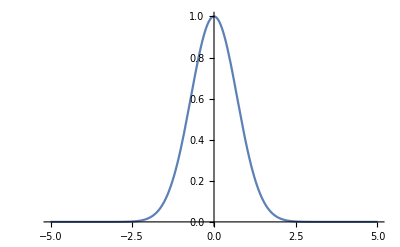

```mathematica
Plot[Exp[-x^2],{x,-5,5}]
```

```mathematica
Plot3D[x^2-2xy-y^2=1,{x,-5,5},{y,-5,5}]
```

Set::write: Tag Plus in -24.9929+24.9929-2 xy is Protected.

-Graphics3D-

```mathematica
Plot3D[4 x^2 Exp[y]-2 x^4-Exp[4y],{x,-3,3},{y,-1,1}]
```

-Graphics3D-

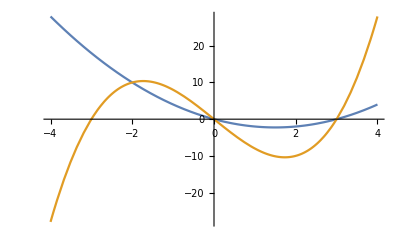

```mathematica
Plot[{t^2-3t,t^3-9t},{t,-4,4}]
```

```mathematica
Plot[{x=t^2-3t,y=t^3-9t},{t,-4,4},{x,-4,4}]
```

Plot::nonopt: Options expected (instead of {x,-4,4}) beyond position 2 in Plot[{x=t^2-3 t,y=t^3-9 t},{t,-4,4},{x,-4,4}]. An option must be a rule or a list of rules.

Plot[{x=t^2-3 t,y=t^3-9 t},{t,-4,4},{x,-4,4}]

#### 8. Solve the following differential equations:

```mathematica
DSolve[{y'[x]==x/(2y[x]),y[1]==1},y[x],x]
```

{{y[x]→(√(1+x^2))/(√2)}}

```mathematica
DSolve[{y'[x]==(-y[x])/x,y[2]==3},y[x],x]
```

{{y[x]→6/x}}

```mathematica
DSolve[{y'[x]==x^2/(y[x])^3,y[0]==1},y[x],x]
```

{{y[x]→((3+4 x^3)^(1/4))/3^(1/4)}}

```mathematica
Simplify[{{y[x]->((3+4 x^3)^(1/4))/3^(1/4)}}]
```

{{y[x]→(1+(4 x^3)/3)^(1/4)}}

```mathematica
DSolve[{x''[t]+5x'[t]+6x[t]==0,x[0]==1,x'[0]==0},x,t]
```

{{x→Function[{t},ⅇ^(-3 t) (-2+3 ⅇ^t)]}}

```mathematica
DSolve[{x''[t]+5x'[t]+6x[t]==Sin[t],x[0]==1,x'[0]==0},x,t]
```

{{x→Function[{t},-1/10 ⅇ^(-3 t) (21-32 ⅇ^t+ⅇ^(3 t) Cos[t]-ⅇ^(3 t) Sin[t])]}}